# Introduction to Mathematica

## A4M36TPJ, WS 15/16, Week 1 & 2

Zdeněk Buk, bukz1@fel.cvut.cz

Dept. of Computer Science and Engineering
Faculty of Electrical Engineering
Czech Technical University in Prague

Last update: Oct 2015

## Preliminaries & Overview

The goal of this lesson is an introduction to Wolfram Mathematica which will be the main tool for solving task and experimenting with various topics in the Programming Language Theory course (A4M36TPJ).

After this lesson you should be able to work with notebooks in Mathematica, write and read basic programs in functional, procedural & rule-based style.

This knowledge is essential for future exercises and tasks in following weeks.

### Installation

CTU students have access to the unlimited license of Wolfram Mathematica, which can be installed on your own computers. This software is also available in computer lab KN-E:310.

Download link: http://download.cvut.cz

### Materials

The course materials and other Information are available at the course website.

https://edux.feld.cvut.cz/courses/A4M36TPJ/

## Introduction

### Getting Started

When you first start Mathematica you should see an empty document called notebook. You can create such document using create new notebook in startup palette or from a menu bar (File ▸ New ▸ Notebook).

-Graphics-

The notebook is divided into cells. Each cell can be assigned with a different style (Title, Subtitle, Text, Input/Output Expression, etc.). For calculations the most important cells are the input and output.

To enter input, just start typing. To evaluate the input, press ⇧[⌤] (or just ⌤ on the numeric keypad). The output cell with result will appear. To enter another input, just continue typing.

-Graphics-

#### Getting Started: Basic Syntax

Mathematica is case sensitive! Built-in functions are capitalized.

Mathematica supports standard arithmetic operators: + (add), - (subtract or unary minus), * (multiply), / (divide), ^ (power).

```mathematica
10+20
```

```mathematica
-10
```

```mathematica
10-20
```

```mathematica
10*20
```

```mathematica
10/20
```

```mathematica
10^20
```

Multiplication can be entered with * operator or you can just follow the number by symbol (without *) or put a single space between two numbers (Mathematica will convert the space into multiplication symbol).

```mathematica
2*4
```

```mathematica
3 4
```

```mathematica
2*a
```

```mathematica
2a
```

Calling functions is the basic way of doing calculations in Mathematica. There are many ways how to call the function, the most general one is to enter the function name followed by square brackets with arguments of the function. If the function has more arguments, they are separated by commas.

```mathematica
Expand[(a+b)^3]
```

```mathematica
N[Pi,20]
```

```mathematica
N[10/20]
```

```mathematica
DateString[]
```

Many common function can be  entered using operators and other special notations. For example, the + operator is internally represented as Plus[x,y]. You can use FullForm function to see the representation of the expression.

```mathematica
x+y
```

```mathematica
FullForm[x+y]
```

```mathematica
FullForm[2x]
```

```mathematica
FullForm[x-y]
```

#### Getting Started: Lists

List is an important data structure in Mathematica, it is used to represent vectors, matrices, data, and in many common inputs and outputs. List is represented by a sequence of elements enclosed in curly braces.

Example: list of three numbers.

```mathematica
{10,20,30}
```

Internal representation is List[10,20,30]

```mathematica
FullForm[{10,20,30}]
```

Following examples shows common uses of lists in various Mathematica computations.

```mathematica
Plot[Sin[x],{x,0,2Pi}]
```

The list {x, 0, 2Pi} specifies that the value of variable x goes from 0 to 2π.

```mathematica
FindMinimum[Sin[x],{x,5}]
```

Find a local minimum, starting at x=5. The output list contains the value of the local minimum (-1) and the position (4.712...). The position is represented by rule → which will be explained in separate chapter.

```mathematica
Table[2^n,{n,0,8}]
```

```mathematica
{10,20,30}+{101,202,303}
```

### Basic Operations

In Mathematica you can define variables and you own functions. You can merge several expressions into one complex computations. In this sections we will show how.

#### Basic Operations: Variables

Using the = sign you can assign value to a variable.

```mathematica
x=5
```

```mathematica
x*y
```

```mathematica
x y
```

```mathematica
2 3
```

```mathematica
xy
```

Be careful to put a space between symbols when the multiplication is needed. The previous example uses symbol “xy” (without any value assigned) except the x multiplied by y.

You can review the definition of the variable by ? operator.

```mathematica
?x
```

Mathematica can use multiple contexts (similar to Java packages) the “Global” in previous output is the default context. We don’t need to go into details about the contexts now.

When definitions are no longer needed it is a good idea to clear them.

```mathematica
Clear[x]
```

After x has been cleared, x represents just a symbol without any value assigned.

```mathematica
x
```

```mathematica
?x
```

#### Basic Operations: Using previous results

When the computation consists of several steps, you can use the results of one step as an input of the following step. This can be done using % symbol which represents the last result (output).

```mathematica
10+20
```

```mathematica
2*%
```

```mathematica
%-100
```

% represents the output of last evaluated expression, not the previous output line. Be careful when evaluating expression in different order.

Another way is to save the current output into variables.

```mathematica
a=10+20
```

```mathematica
b=2*a
```

```mathematica
b-100
```

```mathematica
Clear[a,b]
```

The following example (taken from M101: A First Course in Mathematica) shows the task of counting the occurrences of characters in the nucleoide sequence for a human gene.

First, import the data (string sequence) for the human gene that encodes mitochondrial ribosomal proteins.

The GenomeData requires the Internet connection to import the data from Wolfram database. When executed for the first time, you should see the progress dialog similar to this: -Graphics-

```mathematica
gene=GenomeData["MRPS29P2"]
```

List the individual characters in the string.

```mathematica
chars=Characters[gene]
```

Tally the individual characters, listing each with its multiplicity.

```mathematica
Tally[chars]
```

#### Basic Operations: Sequences of operations

Several steps of the calculation can be organized into a single input by using semicolons to separate the statements.

The semicolon at the end of the input line will hide the output cell.

```mathematica
gene=GenomeData["MRPS29P2"];
chars=Characters[gene];
Tally[chars]
```

```mathematica
Clear[gene,chars]
```

#### Basic Operations: Composing functions

Another way of building up the calculations is by using functions as the arguments of other functions.

```mathematica
Tally[Characters[GenomeData["MRPS29P2"]]]
```

#### Basic Operations: Defining functions

Definitions (as shown in variables section) can also be used to define your own functions.

```mathematica
f[x_]:=x^2+x Sin[x]
```

The underscore in f[x_] is important, it indicates that the argument of f can be anything, not just the literal symbol x.

```mathematica
f[10]
```

```mathematica
f[α]
```

```mathematica
?f
```

```mathematica
Clear[f]
```

#### Basic Operations: Working with lists

There are many functions for working with lists in Mathematica. We create a testing data a show, how to extract parts of the list.

```mathematica
data=Range[1,100,9]
```

```mathematica
Part[data,2]
```

Using negative number we get the part from the tail end of the list.

```mathematica
Part[data,-2]
```

Extract the subset of elements:

```mathematica
Part[data,{1,2,3,4,5}]
```

```mathematica
Part[data,1;;5]
```

```mathematica
Take[data,5]
```

Short notation of Part function:

```mathematica
data[[3]]
```

```mathematica
data[[{1,2,3}]]
```

```mathematica
data[[1;;5]]
```

```mathematica
data[[1;;5;;2]]
```

```mathematica
Clear[data]
```

Complete information about working with list can be found in the guide: List Manipulation ▸

## Programming

### Assignments and Definitions

There are some basic mistakes that the beginners do...

There is underscore missing and assignment (=) is used except delayed assignment (:=). This defines variable f[x] (x is part of the left hand side pattern) with value x^2. The left x and right x are two different things.

```mathematica
Clear[x]
```

```mathematica
f[x]=x^2
```

The following expression doesn’t do the excepted calculation (10^2=100).

```mathematica
f[10]
```

If we take a look on the definition we can see, that the f is defined only for parameter x (symbol “x”) and whee this matches it is replaced by x^2.

```mathematica
?f
```

```mathematica
f[x]
```

If we assign value to x, the situation is even worse. The argument x is evaluated to value 10 and then f[10] is called.

```mathematica
x=10
```

```mathematica
f[x]
```

When we try to define another function g in the same way as f, the situation is different. The difference is in x which has assigned value.

```mathematica
g[x]=x^2
```

```mathematica
?g
```

```mathematica
g[x]
```

```mathematica
g[y]
```

This is not how the functions should work. The correct way of defining the left hand side of the whole definition is to use so-called patterns. The underscore _ represents exactly one element, two underscores __ represent one or more elements, and three underscores ___ represent any number of elements. We can give a name to the pattern adding the symbol (name) before the underscore(s).

```mathematica
s[x_]=x^2
```

```mathematica
?s
```

The last mistake is the usage of assignment (=) which evaluates the right hand side directly (before the definition is constructed). We should use delayed assignment (:=) which evaluates the right hand side when the definition is used.

```mathematica
r[x_]:=x^2
```

```mathematica
?r
```

```mathematica
r[x]
```

```mathematica
r[10]
```

```mathematica
r[y]
```

```mathematica
Clear[x,f,g,h,r,s]
```

Another example of delayed assignment:

```mathematica
rand1=RandomReal[];
rand2:=RandomReal[];
```

```mathematica
Table[rand1,{5}]
```

```mathematica
Table[rand2,{5}]
```

```mathematica
Clear[rand1,rand2]
```

### Procedural Programming

Procedural programming means programming using loops, if-statements, and other functions that control the flow of execution through a program. For example, a compound expression (a sequence of statements separated by semicolons) is a procedural program. In a compound expression the flow of execution is to simply evaluate statements in the order given.

```mathematica
gene=GenomeData["MRPS29P2"];
chars=Characters[gene];
Tally[chars]
```

{{A,150},{T,132},{G,131},{C,102}}

One of the most common procedural constructs is the if control structure. In Mathematica, the If function has the following syntax: If[test,then,else]

The following example demonstrates how the flow of execution depends on the result of the test x>π.

```mathematica
f[x_]:=If[x>π,
Print[x," is larger than π"],
Print[x," is not larger than π"]
]
```

```mathematica
f[E]
```

ⅇ is not larger than π

The basic elements of procedural programming are functions used for:

evaluating a sequence of expressions (called a compound expression):

expr_1;expr_2;expr_3;…

loops:

Do, For, While, Table, …

branching (or jumping), depending on a test or condition:

If, Which, Switch

#### Example

Program that computes the sum of the integers 1 through n.

```mathematica
n=10;
result=0;
Do[result=result+k,{k,1,n}];
result
```

```mathematica
Clear[n]
```

By putting this program on the right side of an assignment, this program can become the definition of a function.

```mathematica
f[n_]:=(
result=0;
Do[result=result+k,{k,1,n}];
result
)
```

You “run” this program by evaluating an expression that matches f[n_].

```mathematica
f[10]
```

55

Our function expects a positive integer as the argument. It can give incorrect or unexpected results if the argument is not a positive integer.

```mathematica
f[-2]
```

0

Here is a modification of this program, which checks that n is a positive integer before doing the calculation.

```mathematica
f[n_]:=If[IntegerQ[n]&&n>0,
result=0;
Do[result=result+k,{k,1,n}];
result,
Print[n, " is not a positive integer."]
]
```

```mathematica
f[Pi]
```

π is not a positive integer.

```mathematica
f[-9]
```

-9 is not a positive integer.

```mathematica
f[9]
```

45

When assignments to temporary variables are used for keeping track of intermediate results, it is common practice, especially in larger programs, to localize those variables to avoid conflicts with other parts of the program.

```mathematica
result=100
```

100

```mathematica
f[10]
```

55

The original value of result is lost:

```mathematica
result
```

55

Variables can be localized using the Module function. The first argument in Module is a list of variables to localize, and the second argument is the expression to evaluate.

Module[{vars},
body_of _function
…]

Here is a definition in which the variable result is localized using Module.

```mathematica
f[n_]:=Module[{result},
result=0;
Do[result=result+k,{k,1,n}];
result
]
```

With this definition, evaluation of f will leave existing values of result unchanged.

```mathematica
result=100
```

100

```mathematica
f[10]
```

55

```mathematica
result
```

100

Variables that have not been localized are called global variables.

```mathematica
Clear[f,result]
```

### Functional Programming

Functional programing guide

... programming using functions as the arguments of other functions. In this paradigm, computation is viewed as the evaluation of functions.

```mathematica
Tally[Characters[GenomeData["MRPS29P2"]]]
```

Consider the task of computing the future value of a principal amount using the formula for compound interest (http://en.wikipedia.org/wiki/Compound_interest). As a concrete example, consider an interest rate of 3% compounded monthly.

```mathematica
value[p_]:=p(1+3/(100 12))
```

If you start with $1000, this gives the value of your account after one month.

```mathematica
value[1000.]
```

1002.5

Here is the value after two months.

```mathematica
value[value[1000.]]
```

And after three months...

```mathematica
value[value[value[1000.]]]
```

The Nest function is used to iterate functions.

```mathematica
Clear[f];
Nest[f,Subscript[x, 0],5]
```

f[f[f[f[f[x_0]]]]]

Future value in our example can be simply done using the function Nest.

```mathematica
Nest[value,1000.,3]
```

1007.52

Here are all the intermediate values.

```mathematica
NestList[value,1000.,3]
```

{1000.,1002.5,1005.01,1007.52}

... and for the first 12 months.

```mathematica
NestList[value,1000.,12]
```

{1000.,1002.5,1005.01,1007.52,1010.04,1012.56,1015.09,1017.63,1020.18,1022.73,1025.28,1027.85,1030.42}

#### Map

The basic behavior of Map:

```mathematica
Map[f,{1,2,3}]
```

{f[1],f[2],f[3]}

```mathematica
Map[f,List[1,2,3]]
```

{f[1],f[2],f[3]}

```mathematica
Map[f,g[1,2,3]]
```

g[f[1],f[2],f[3]]

```mathematica
Map[f,a+b+c]
```

f[a]+f[b]+f[c]

Data filtering example: replace all small values by zero.

```mathematica
data={1,2,3.14,0.5,0.1,-0.9,-2,0};
```

```mathematica
f[x_]:=If[Abs[x]<1,0,x]
```

```mathematica
f[0.5]
```

0

```mathematica
f[1.5]
```

1.5

```mathematica
ParallelMap[f,data]
```

{1,2,3.14,0,0,0,-2,0}

```mathematica
Clear[data,f]
```

#### Expressions

The head of an atomic expression is simply the type of object that it is. The FullForm of an atomic expression is simply that expression.

```mathematica
{Head[42],FullForm[42]}
```

{Integer,42}

```mathematica
{Head[x],FullForm[x]}
```

{Symbol,x}

```mathematica
{Head["Hello"],FullForm["Hello"]}
```

{String,"Hello"}

Compound expressions are built up from atomic expressions, they have a head and zero or more elements. Compound expressions are usually called normal expressions. All normal expressions are of the following form:

h[e_1,e_2,…,e_n]

The h is called the head of the expression and the e_i are the elements. Both the head and the elements of a normal expression can be either atomic expressions or normal expressions themselves.

For example, the expression f[a,b,c] is a normal expression with head f and with three (atomic) elements. The Head function returns the head of its argument.

```mathematica
f[a,b,c]//Head
```

f

```mathematica
f[a,b,c]//Length
```

3

With Part, you can extract any elements.

```mathematica
Part[f[a,b,c],2]
```

b

Example: Nested list of lists, a matrix.

```mathematica
mat={{a,b},{d,e},{g,h}}
```

{{a,b},{d,e},{g,h}}

The FullForm or TreeForm of mat shows its structure.

```mathematica
FullForm[mat]
```

List[List[a,b],List[d,e],List[g,h]]

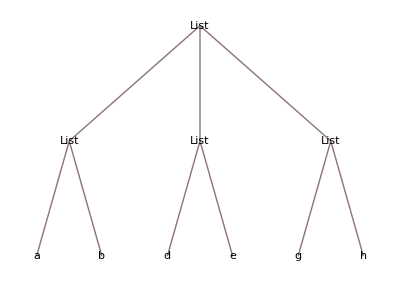

```mathematica
TreeForm[mat]
```

```mathematica
Head[mat]
```

List

Each of the elements of mat is a list of length 2; there are three of them.

```mathematica
Length[mat]
```

3

Extract elements of the expression.

```mathematica
Part[mat,2]
```

More complicated example.

```mathematica
expr=a^(c+1)+10a b+b^3
```

```mathematica
TreeForm[expr]
```

```mathematica
expr[[2]]
```

```mathematica
Part[expr,2]
```

```mathematica
Clear[expr,mat]
```

#### Apply

Apply[f,expr] replaces the head of expr with f.

Basically, think of using Map when you want to operate on the elements of an expression; use Apply when you want to change the structure of the expression.

Basic behavior of Apply:

```mathematica
Apply[f,g[1,2,3]]
```

f[1,2,3]

```mathematica
Apply[Times,{a,b,c}]
```

a b c

Using this approach, here is how you might compute 10!

```mathematica
Apply[Times,{1,2,3,4,5,6,7,8,9,10}]
```

3628800

```mathematica
Apply[Times,Range[10]]
```

3628800

Functional approach to adding up the first 10 integers.

```mathematica
Apply[Plus,Range[10]]
```

55

```mathematica
Total[Range[10]]
```

55

#### Example

Finding the largest element in each row of the matrix.

```mathematica
mat={{1,2,3},{4,3,2},{1,9,5}};
```

```mathematica
MatrixForm[mat]
```

(1 | 2 | 3
4 | 3 | 2
1 | 9 | 5)

Procedural program:

```mathematica
result={};
Do[
result=Append[result,Max[mat[[k]]]],
{k,1,3}
];
result
```

{3,4,9}

Functional approach:

```mathematica
Map[Max,mat]
```

{3,4,9}

```mathematica
Clear[result,mat]
```

### Rule-based Programming

Recall that when you make an assignment to a symbol, the value of that symbol is automatically substituted into any expression containing that symbol.

```mathematica
x=5
```

5

```mathematica
x^2+x y
```

25+5 y

Replacement rules can be used to make substitutions in other expressions without assigning values to symbols. For example, x→5 represents a rule for replacing x by 5. The → operator is entered by typing - followed by >.

This input uses the ReplaceAll function and the rule x→5 to make a substitution for x in the expression...

```mathematica
Clear[x]
```

```mathematica
ReplaceAll[x^2+x y,x->5]
```

25+5 y

The basic syntax of ReplaceAll is:

ReplaceAll[expr,pattern→replacement]

Here is the same input using the shorthand /. operator for ReplaceAll.

```mathematica
x^2+x y/.x->5
```

25+5 y

The basic syntax for the shorthand notation is:

expr/.pattern→replacement

The replacement rule does not assign any value to x.

```mathematica
?x
```

Global`x

An example of replacement on strings:

```mathematica
StringReplace["Which witch wished which wicked wish?","w"->"W"]
```

Which Witch Wished Which Wicked Wish?

#### Patterns

The expression on the left side of a rule or assignment is a pattern. Patterns can be constructed to match any class of expressions.

Pattern | Expression that match | Example
_ | Any expression | x, "text", 42
_Real | Expression with head Real | 1.23
_?Negative | Expression that passes the Negative test | -42
{_,_} | List of two expressions | {x,123}

The pattern _ (the underscore character) matches any expression.

```mathematica
Cases[{2,g[z],π,3.4,-5,{a,b}},_]
```

{2,g[z],π,3.4,-5,{a,b}}

Named patterns: the pattern x_ gives the matched expression the name x, so that expression can be used elsewhere in the rule.

Matching heads:

```mathematica
Cases[{2,g[z],π,3.4,-5,{a,b}},_Real]
```

{3.4}

```mathematica
Cases[{2,g[z],π,3.4,-5,{a,b}},_Symbol]
```

{π}

```mathematica
Head[g[z]]
```

g

Matching with predicates: the pattern x_/;Negative[x] matches any negative number. It can be read as, “the pattern named x under the condition that x passes the Negative test”.

```mathematica
Cases[{2,g[z],π,3.4,-5,{a,b}},n_/;Negative[n]]
```

{-5}

a shorthand notation:

```mathematica
Cases[{2,g[z],π,3.4,-5,{a,b}},_?Negative]
```

{-5}

Matching a pair: the pattern {p_,q_} matches any list containing any two expressions.

```mathematica
Cases[{2,g[z],π,3.4,-5,{a,b}},{p_,q_}]
```

{{a,b}}

#### Pattern matching

Previously shown example of checking arguments of the function...

```mathematica
f[n_]:=If[IntegerQ[n]&&n>0,
result=0;
Do[result=result+k,{k,1,n}];
result,
Print[n, " is not a positive integer."]
]
```

...can be redefined using patterns:

```mathematica
Clear[f]
```

```mathematica
f[n_Integer?Positive]:=Module[
{result=0},
Do[result=result+k,{k,1,n}];
result
]
```

```mathematica
?f
```

Global`f

f[n_Integer?Positive]:=Module[{result=0},Do[result=result+k,{k,1,n}];result]

```mathematica
f[-1]
```

f[-1]

```mathematica
f[π]
```

f[π]

```mathematica
f[10]
```

55

```mathematica
Clear[f]
```

#### Pattern examples

Extract all integers

```mathematica
Cases[{1,-2,-3.14,42,3.14,x},_Integer]
```

{1,-2,42}

Replace all integers by 0

```mathematica
{1,-2,-3.14,42,3.14,x}/._Integer->0
```

{0,0,-3.14,0,3.14,x}

Extract all elements that pass the Negative test

```mathematica
Cases[{1,-2,-3.14,42,3.14,x},_?Negative]
```

Replace all negative numbers by 0

```mathematica
{1,-2,-3.14,42,3.14,x}/._?Negative->0
```

Reverse the elements in all lists of two elements

```mathematica
{{1,2},{3,4},{5,6},{7,8}}/.{p_,q_}->{q,p}
```

{{2,1},{4,3},{6,5},{8,7}}

### Comparing Programming Styles

Nearly all nontrivial programs use a mixture of programming styles. No one style is always better than another. You should choose whatever programming style seems most natural for you or for what you want to do.

#### Example

Given a list of pairs of numbers, return a list consisting of the sum of each pair.

```mathematica
pairs={{1,2},{10,20},{100,200},{1,100},{2,200}};
```

procedural approach

```mathematica
result=Table[Null,{Length[pairs]}];
Do[result[[k]]=First[pairs[[k]]]+Last[pairs[[k]]],
{k,1,Length[pairs]}]
result
```

{3,30,300,101,202}

structured procedure using Table

```mathematica
Table[pairs[[k,1]]+pairs[[k,2]],{k,Length[pairs]}]
```

{3,30,300,101,202}

functional approaches

```mathematica
Map[Total,pairs]
```

{3,30,300,101,202}

```mathematica
Total[Transpose[pairs]]
```

{3,30,300,101,202}

rule-based approach

```mathematica
pairs/.{p_,q_}->p+q
```

{3,30,300,101,202}

## Exercises

### Programming Style

Evaluate the following expression to define data to be a list of pairs of elements.

```mathematica
data={{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5}};
```

Here is a procedural program that reverses the elements in each pair. Evaluate this input to get the result. This program works by initializing a list in which all the elements are Null and then assigning each element in that list to be the reverse of the corresponding element from data.

```mathematica
result=Table[Null,{Length[data]}];
Do[
result[[k]]=Reverse[data[[k]]],
{k,1,Length[data]}
];
result
```

{{y1,x1},{y2,x2},{y3,x3},{y4,x4},{y5,x5}}

Create a functional program that gives the same result.

```mathematica
Map[Reverse, data]
```

{{y1,x1},{y2,x2},{y3,x3},{y4,x4},{y5,x5}}

```mathematica
Reverse[data, 2]
```

{{y1,x1},{y2,x2},{y3,x3},{y4,x4},{y5,x5}}

Create a rule-based program that gives the same result.

```mathematica
data /. {p_, q_} -> {q, p}
```

{{y1,x1},{y2,x2},{y3,x3},{y4,x4},{y5,x5}}

Modify these programs (procedural, functional, rule-based) so that the result is a list of the first element in each pair. For data, the result from each program will be {x1,x2,x3,x4,x5}.

```mathematica
result=Table[Null,{Length[data]}];
Do[
result[[k]]=First[data[[k]]],
{k,1,Length[data]}
];
result
```

{x1,x2,x3,x4,x5}

```mathematica
Map[First, data]
```

{x1,x2,x3,x4,x5}

```mathematica
data /. {p_, q_} -> p
```

{x1,x2,x3,x4,x5}

Now modify these programs (procedural, functional, rule-based) so that each program returns a list containing the sum of the elements in each pair.

```mathematica
result=Table[Null,{Length[data]}];
Do[
result[[k]]=Total[data[[k]]],
{k,1,Length[data]}
];
result
```

{x1+y1,x2+y2,x3+y3,x4+y4,x5+y5}

```mathematica
Map[Total, data]
```

{x1+y1,x2+y2,x3+y3,x4+y4,x5+y5}

```mathematica
data /. {p_, q_} -> p+q
```

{x1+y1,x2+y2,x3+y3,x4+y4,x5+y5}

### Debugging a Procedural Program

Evaluate the following input to define a function f that takes a matrix as an argument. This function is intended to return the row from that matrix for which the first element has the largest absolute value.

```mathematica
f[m_]:=Module[{result},
{result=m[[1]];
Do[
If[Abs[m[[k,1]]]>Abs[result[[1]]],
result=m[[k]]],
{k,2,Length[m]}
]
result}
]
```

Evaluate the following input and note that this program does not do what it is intended to do. It returns the correct row from the matrix, but each element in that row is multiplied by Null, and that row is enclosed in an unwanted list.

```mathematica
f[({{1, 4, 7}, {9, 1, 8}, {4, 6, 1}, {11, 5, 8}, {6, 1, 1}})]
```

{{11 Null,5 Null,8 Null}}

Correct the two errors in this program so that the result for the example is {11,5,8}.